Info on the notebook:
This notebook uses the BiGONLight package to compute observables in Newtonian Plane-parallel model.
It is structured as follows: 
- model set-up:  give the 4D metric tensor components as input and compute the 3+1 quantities lapse α, shift β^i, spatial metric γ_ij, extrinsic curvature K_ij and the normal vector n^μ;
- geodesic: provide initial position and tangent vector {x^μ, ℓ^μ} as input to find null geodesics;
- parallel transported frame: give the initial conditions for a frame (ϕ^μ)_αthat will be parallel transported along the computed geodesic (we use the SNF, i.e. (ϕ^μ)_α={u^μ,(ϕ^μ)_1,(ϕ^μ)_2, ℓ^μ} with u^μ the four-velocity and (ϕ^μ)_A two orthonormal vectors)
- optical tidal matrix: compute the optical tidal matrix (R^μ)_ρσν ℓ^ρ ℓ^σ in the parallel propagated frame; 
- BGO: compute and solve the Geodesic Deviation Equation for the Bi-local Geodesic Operators along the null geodesic;
- observables: compute the optical observables in the BGO framework: redshift, redshift drift, angular diameter distance, luminosity distance, parallax distance, distance slip, convergence and shear.

Set the current directory as working directory and load the package.

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["bigonlight6`"]
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`70."&);
```

a generic direction can be written as 𝓋^μ=𝓋^0∂_0 +ψ(sinχ cosξ ∂_1 +sinχ sinξ ∂_1 +cosχ ∂_3)=(𝓋^0(∂_0))^μ+ψ (N⃗)^μ with respect to the local tetrad ∂_μ . 
In particular for a null direction 𝓋^0=±1 and ψ=1 , while for a timelike direction 𝓋^0=±c γ and ψ=c γ β  where β=vel/c the normalized velocity and γ=1/(√(1-β^2)) the Lorentz factor.


 Doing calculations there is always the risk that the kernel quits and all the data are lost. 
To avoid that, it is possible  to save the BGOs using the command :

Join[XXgroup,XLgroup]>>"GBO_data.m" 

Now, the BGOs are saved in a file and eventually they can be imported running the command:

 BGO=<<"GBO_data.m";
 
 In this way, even if the kernel quits, the BGOs are saved and we save time!!!!

```mathematica
𝒱[Vt_,lorentz_,direction1_,direction2_]:=
Module[{V0=Vt, γ=lorentz,χ=direction1,ξ=direction2},
V0{1,0,0,0}+γ(Sin[χ]Cos[ξ]{0,1,0,0}+Sin[χ]Sin[ξ]{0,0,1,0}+Cos[χ]{0,0,0,1})
]
```

```mathematica
StandardPlotStyle[size_,sizelegend_,ylabel_,xlabel_,title_,legend_,position_]:=Module[{ft=size,ftL=sizelegend,yL=ylabel,xL=xlabel,pt=title,list=legend,pl=position},
If[ list=={},{FrameLabel->{{yL,""},{xL,""}},Frame->True,FrameTicks->True,FrameStyle->Directive[FontSize->ft],GridLines->Automatic,GridLinesStyle->Directive[Gray,Opacity[0.2],Dashed],PlotLabel->Style[pt,Bold,FontSize->ft]},{FrameLabel->{{yL,""},{xL,""}},Frame->True,FrameTicks->True,FrameStyle->Directive[FontSize->ft],GridLines->Automatic,GridLinesStyle->Directive[Gray,Opacity[0.2],Dashed],PlotLabel->Style[pt,Bold,FontSize->ft],PlotLegends->Placed[LineLegend[Table[Style[list[[m]],FontSize->ftL],{m,1,Length[list]}]],pl]},Print["Error"]]];
```

# Newtonian

In this notebook we use geometric units G=c=1. This allows us to express mass, length and  time as the same unit. For our convenience, we will express all quantities as dimension-less quantities in units of length L. Therefore, any physical quantity Q^phys=Q^comp L^α where α is a certain exponent and Q^comp is dimensionless. 
The dynamics of this model splits into a flat ΛCDM background and a non-linear dynamics for the inhomogeneities. 
Therefore, we choose to use the ΛCDM background to set-up the characteristic length L  equal to the conformal time today in Mpc η_0==L .
From Friedmann equation, η=1/ℋ_0∫(a^(-1/2)ⅆa)/((Ω_m0+Ω_Λ a^3)^(1/2)) , solving the integral and using a_0==1, we finally have L=η_0=14415.175 Mpc
The dimensionless computational present time and the dim-less hubble constant are η_0^comp==η_0/L==1  and  𝒽_0^comp==ℋ_0 L==2.246 10^-4  
Knowing the conformal time as function of the scale factor η(a), we can use the expression for the redshift in FLRW, 
									z+1=a_𝒪/a 
to find the value of a_in corresponding to a given z_in. Then the initial conformal time is found as η_in==η(a_in).
 Alternatively, one can use a specific value for a_in, like the one we used here  a_in== a_EdS==10^-4.

## Units and Parameters

```mathematica
L=(EllipticF[ArcCos[((1+(1-Sqrt[3])1(ΩΛ/Ωm0)^(1/3))/(1+(1+Sqrt[3])1(ΩΛ/Ωm0)^(1/3)))/.{Ωm0->0.3153, ΩΛ->0.6847}],(2+Sqrt[3])/4]/((H0 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3))/.{Ωm0->0.3153, ΩΛ->0.6847,H0->67.36/299792.458})) (*Mpc*)

𝒽0=(EllipticF[ArcCos[((1+(1-Sqrt[3])1(ΩΛ/Ωm0)^(1/3))/(1+(1+Sqrt[3])1(ΩΛ/Ωm0)^(1/3)))/.{Ωm0->0.3153, ΩΛ->0.6847}],(2+Sqrt[3])/4]/(( 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3))/.{Ωm0->0.3153, ΩΛ->0.6847})) 
ηin=(EllipticF[ArcCos[((1+(1-Sqrt[3])1/11(ΩΛ/Ωm0)^(1/3))/(1+(1+Sqrt[3])1/11(ΩΛ/Ωm0)^(1/3)))/.{Ωm0->0.3153, ΩΛ->0.6847}],(2+Sqrt[3])/4]/(( 3^(1/4)𝒽0(ΩΛ)^(1/6)(Ωm0)^(1/3))/.{Ωm0->0.3153, ΩΛ->0.6847}))
ETA0=1
START=TimeObject[Now]
```

14415.1749294347360096684854207765183902700577486166574583760745894401

3.23892798946504457297344410826874863799472597121445278785569843903373

0.3315276791953745270775203618502639578667677121831107407037375850273

1

10:24:42GMT+2.TimeObject[{10,24,42.336677},TimeZone→2.]

The free-function of the model is the gravitational potential ϕ_0 that specifies the spatial distribution of the wall inhomogeneities . In this notebook, we use a sinusoidal form for the gravitational potential, defined as:

									ϕ_0[x]=ℐ Sin[(2π)/k x]
with inhomogeneities periodic over a scale k = 100 Mpc and with intensity ℐ defined setting the value of the maximum of the  density contrast today  equal to δ_0^max==1.

The form of the density contrast δ^PN is the one in Eq. (10) in Grasso et.al. (2021)
Note that we  normalise 𝒟[η_0]=1 and that the computational value for k is k^comp=k^phys/L==100/L.

```mathematica
λ100=100/L;
P100=First[P/.Solve[Evaluate[((2/3 1/((𝒽0)^2 Ωm0) P ((2π)/λ100)^2)/(1-2/3(P ((2π)/λ100)^2)/((𝒽0)^2 Ωm0))+1/c^2 1/((1-2/3(P ((2π)/λ100)^2)/((𝒽0)^2 Ωm0))^2)(5/9(3-4 anl) ( P ((2π)/λ100))^2/((𝒽0)^2 Ωm0)+20/9(2-anl) 1/((𝒽0)^2 Ωm0)(P P ((2π)/λ100)^2)+20/21( 2/3 1/((𝒽0)^2 Ωm0))^2(( P ((2π)/λ100))^2 P ((2π)/λ100)^2)))/.{Ωm0->0.3153, ΩΛ->0.6847,anl->0.46,c->1}]==1,P]]
x0=0
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

3.0239848588247076568010487112526165589981117488081730229554377492437×10^-6

```mathematica
param={ω->(2π)/λ100,Amp->P100,Ωm0->0.3153, ΩΛ->0.6847, c->1, anl->0.46}(*anl->0.46 correspiond to Subscript[f, nl]==-0.9 from Plank2018 (local fnl from arxiv:1905.05697)*)
(*param={ω->(2π)/λ500,Amp->P500,Ωm0->0.3153, ΩΛ->0.6847, c->1, anl->1.48}*)(*arXiv:1807.06209 (Tab 2 5th column) , H0 units: km/s(Mpc)^-1. Regarding anl I have used "A&A 594,A17 (2016)" since the results from Plank2018 have to be published jet: Subscript[f, nl]==0.8-> Subscript[f, nl]==5/3(Subscript[a, nl]-1)-> Subscript[a, nl]==3/5 Subscript[f, nl]+1*)
```

{ω→905.732153170478655912117410485725091337521215109253757757276619318621,Amp→3.0239848588247076568010487112526165589981117488081730229554377492437×10^-6,Ωm0→0.3153,ΩΛ→0.6847,c→1,anl→0.46}

## Model set-up

We need to provide the spacetime metric g_μν. 
This can be done in two ways: 
		1)  writing the analytic expression for the metric components g_μν=(g_00 | g_01 | g_02 | g_03
g_10 | g_11 | g_12 | g_13
g_20 | g_21 | g_22 | g_23
g_30 | g_31 | g_32 | g_33) 
		2) import data from a (relativistic) numerical simulation. 
		
In this case, we know the form of the metric g_μν, so we use the first method.

```mathematica
Clear[A,𝒟,ϕ,ℋ,ℱ,γN11,γPN11,γaa]
```

```mathematica
Clear[α,β,g,K,g4,X,V,e,Energy,nd,nu,x,y,z,η]
```

```mathematica
X4={η,x,y,z};
X={x,y,z};
V={v1,v2,v3};
e={e1,e2,e3};
Energy={energy, affine};
```

```mathematica
g4={{-(A[η])^2,0,0,0},{0,(A[η])^2(γN11[η,x]+1/c^2 γPN11[η,x]),0,0},{0,0,(A[η])^2(1+1/c^2 γaa[η,x]),0},{0,0,0,(A[η])^2(1+1/c^2 γaa[η,x])}};
```

```mathematica
solADM=ADM[g4,X4];
α=Evaluate[solADM[[1]]]
β=Evaluate[solADM[[2]]]
g=Evaluate[solADM[[3]]]
K=Evaluate[solADM[[4]]]
nu=Evaluate[solADM[[5]]]
nd=Evaluate[solADM[[6]]]
```

√(A[η]^2)

{0,0,0}

{{A[η]^2 (γN11[η,x]+γPN11[η,x]/c^2),0,0},{0,A[η]^2 (1+γaa[η,x]/c^2),0},{0,0,A[η]^2 (1+γaa[η,x]/c^2)}}

{{-(√(A[η]^2) (2 c^2 γN11[η,x] A'[η]+2 γPN11[η,x] A'[η]+A[η] (c^2 γN11^(1,0)[η,x]+γPN11^(1,0)[η,x])))/(2 c^2 A[η]),0,0},{0,-(√(A[η]^2) (2 (c^2+γaa[η,x]) A'[η]+A[η] γaa^(1,0)[η,x]))/(2 c^2 A[η]),0},{0,0,-(√(A[η]^2) (2 (c^2+γaa[η,x]) A'[η]+A[η] γaa^(1,0)[η,x]))/(2 c^2 A[η])}}

{1/(√(A[η]^2)),0,0,0}

{-√(A[η]^2),0,0,0}

```mathematica
αα[τ_]:=α/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
ββ[τ_]:=β/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
VV[η_]:=Table[V[[i]][η],{i,1,Length[X]}];
gg[τ_]:=g/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
gg4[τ_]:=g4/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
nup[τ_]:=nu/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
ndown[τ_]:=nd/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];

αlup[η_]:=(*EBG[η]*)αα[η] (nup[η]+Flatten[{0,VV[η]}]);
αldown[η_]:=(*EBG[η]*)αα[η](ndown[η]+Flatten[{0,gg[η].VV[η]}]);
```

## Geodesic

```mathematica
geod=GeodesicEquations[X,V,g,K,α,β,η]
```

{x'[η]==√(A[η]^2) v1[η],v1'[η]==√(A[η]^2) ((v2[η]^2 γaa^(0,1)[η,x[η]])/(2 (c^2 γN11[η,x[η]]+γPN11[η,x[η]]))+(v3[η]^2 γaa^(0,1)[η,x[η]])/(2 (c^2 γN11[η,x[η]]+γPN11[η,x[η]]))-(v1[η]^2 (c^2 γN11^(0,1)[η,x[η]]+γPN11^(0,1)[η,x[η]]))/(2 c^2 γN11[η,x[η]]+2 γPN11[η,x[η]])-(√(A[η]^2) v1[η] (2 c^2 γN11[η,x[η]] A'[η]+2 γPN11[η,x[η]] A'[η]+A[η] (c^2 γN11^(1,0)[η,x[η]]+γPN11^(1,0)[η,x[η]])))/(c^2 A[η]^3 (γN11[η,x[η]]+γPN11[η,x[η]]/c^2))+v1[η] ((√(A[η]^2) v2[η]^2 (2 (c^2+γaa[η,x[η]]) A'[η]+A[η] γaa^(1,0)[η,x[η]]))/(2 c^2 A[η])+(√(A[η]^2) v3[η]^2 (2 (c^2+γaa[η,x[η]]) A'[η]+A[η] γaa^(1,0)[η,x[η]]))/(2 c^2 A[η])+(√(A[η]^2) v1[η]^2 (2 c^2 γN11[η,x[η]] A'[η]+2 γPN11[η,x[η]] A'[η]+A[η] (c^2 γN11^(1,0)[η,x[η]]+γPN11^(1,0)[η,x[η]])))/(2 c^2 A[η]))),y'[η]==√(A[η]^2) v2[η],v2'[η]==√(A[η]^2) (-(v1[η] v2[η] γaa^(0,1)[η,x[η]])/(c^2+γaa[η,x[η]])-(√(A[η]^2) v2[η] (2 (c^2+γaa[η,x[η]]) A'[η]+A[η] γaa^(1,0)[η,x[η]]))/(c^2 A[η]^3 (1+γaa[η,x[η]]/c^2))+v2[η] ((√(A[η]^2) v2[η]^2 (2 (c^2+γaa[η,x[η]]) A'[η]+A[η] γaa^(1,0)[η,x[η]]))/(2 c^2 A[η])+(√(A[η]^2) v3[η]^2 (2 (c^2+γaa[η,x[η]]) A'[η]+A[η] γaa^(1,0)[η,x[η]]))/(2 c^2 A[η])+(√(A[η]^2) v1[η]^2 (2 c^2 γN11[η,x[η]] A'[η]+2 γPN11[η,x[η]] A'[η]+A[η] (c^2 γN11^(1,0)[η,x[η]]+γPN11^(1,0)[η,x[η]])))/(2 c^2 A[η]))),z'[η]==√(A[η]^2) v3[η],v3'[η]==√(A[η]^2) (-(v1[η] v3[η] γaa^(0,1)[η,x[η]])/(c^2+γaa[η,x[η]])-(√(A[η]^2) v3[η] (2 (c^2+γaa[η,x[η]]) A'[η]+A[η] γaa^(1,0)[η,x[η]]))/(c^2 A[η]^3 (1+γaa[η,x[η]]/c^2))+v3[η] ((√(A[η]^2) v2[η]^2 (2 (c^2+γaa[η,x[η]]) A'[η]+A[η] γaa^(1,0)[η,x[η]]))/(2 c^2 A[η])+(√(A[η]^2) v3[η]^2 (2 (c^2+γaa[η,x[η]]) A'[η]+A[η] γaa^(1,0)[η,x[η]]))/(2 c^2 A[η])+(√(A[η]^2) v1[η]^2 (2 c^2 γN11[η,x[η]] A'[η]+2 γPN11[η,x[η]] A'[η]+A[η] (c^2 γN11^(1,0)[η,x[η]]+γPN11^(1,0)[η,x[η]])))/(2 c^2 A[η])))}

```mathematica
enereq=EnergyEquations[g,K,α,β,Energy,X,V,η]
```

{energy'[η]==√(A[η]^2) energy[η] (-(√(A[η]^2) v2[η]^2 (2 (c^2+γaa[η,x[η]]) A'[η]+A[η] γaa^(1,0)[η,x[η]]))/(2 c^2 A[η])-(√(A[η]^2) v3[η]^2 (2 (c^2+γaa[η,x[η]]) A'[η]+A[η] γaa^(1,0)[η,x[η]]))/(2 c^2 A[η])-(√(A[η]^2) v1[η]^2 (2 c^2 γN11[η,x[η]] A'[η]+2 γPN11[η,x[η]] A'[η]+A[η] (c^2 γN11^(1,0)[η,x[η]]+γPN11^(1,0)[η,x[η]])))/(2 c^2 A[η])),affine'[η]==(√(A[η]^2))/energy[η]}

Specify the functions used in the metric

```mathematica
Clear[A,𝒟,ϕ,ℋ]
```

```mathematica
A[η_]=((Ωm0/ΩΛ)^(1/3)((1-JacobiCN[( 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3)) 𝒽0 η ,(2+Sqrt[3])/4])/(-1+√3+(1+√3) JacobiCN[( 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3)) 𝒽0 η ,(2+Sqrt[3])/4])))/.param(*from 1109.2258*);
normalizzazione=5/2 Ωm0-((5/2 Ωm0)-(A[η]Sqrt[1+ΩΛ/Ωm0 A[η]^3]Hypergeometric2F1[3/2,5/6,11/6,-ΩΛ/Ωm0 A[η]^3])/.η->ETA0)/.param;
𝒟[η_]=(A[η]/(normalizzazione)Sqrt[1+ΩΛ/Ωm0 A[η]^3]Hypergeometric2F1[3/2,5/6,11/6,-ΩΛ/Ωm0 A[η]^3])/.param;
ϕ[x_]=(Amp Sin[ω  x])/.param;
γN11[η_,x_]:=(1-(2 𝒟[η] ϕ''[x])/(3 (𝒽0)^2 Ωm0))^2/.param
γPN11[η_,x_]:=((-(10 ϕ[x])/3+(4 anl-5)(10  𝒟[η] ϕ'[x]^2)/(9 (𝒽0)^2 Ωm0)+(anl-1)(40  𝒟[η] ϕ[x] ϕ''[x])/(9 (𝒽0)^2 Ωm0)+20/27(41/7-4anl)(𝒟[η]^2 ϕ'[x]^2 ϕ''[x])/((𝒽0)^4 Ωm0^2)+40/27(3-2 anl)(𝒟[η]^2 ϕ[x] ϕ''[x]^2)/((𝒽0)^4 Ωm0^2)-(80 𝒟[η]^3 ϕ'[x]^2 ϕ''[x]^2)/(189 (𝒽0)^6 Ωm0^3)))/.param;
γaa[η_,x_]:=((10/9((𝒟[η] ϕ'[x]^2)/((𝒽0)^2 Ωm0)-3 ϕ[x])))/.param;
```

### Initial conditions

The initial conditions can be given in two different ways:
1) directly specifying the values or
2) giving the initial direction v^2 and v^3 and use the function InitialConditions[] to compute v^1 such that the geodesic is null.

```mathematica
κ=SetPrecision[(*A[ηin]^-2*)𝒱[-1,1,π/4,π/4],70]
TimeObject[Now]
```

{-1.,0.5,0.5,0.7071067811865475244008443621048490392848359376884740365883398689953662}

10:25:35GMT+2.TimeObject[{10,25,35.866323},TimeZone→2.]

```mathematica
(g4.κ.κ)/.{η->ETA0,x->x0,y->0,z->0}/.param
```

-1.007974908477171727322294607764548702412443982065197821472×10^-7+0. ⅈ

The vector κ^μ must be expressed in 3+1 form κ^μ=E(n^μ+V^μ) where E=-κ^μ n_μ and V^μ=κ^μ/E-n^μ

```mathematica
ϵ=SetPrecision[-∑_(i=1)^4 κ[[i]]nd[[i]]/.{η->ETA0,x->x0,y->0,z->0},70]
vi=SetPrecision[Table[(κ[[i]]/ϵ-nu[[i]])/.{η->ETA0,x->x0,y->0,z->0},{i,1,4}],70]
```

-1.

{0,-0.4999999999999999999999999999999999999999999999999999999999999999999999,-0.4999999999999999999999999999999999999999999999999999999999999999999999,-0.7071067811865475244008443621048490392848359376884740365883398689953661}

```mathematica
substitution={η->ETA0,x->x0,y->0,z->0,v2->vi[[3]],v3->vi[[4]]};
```

```mathematica
initialvel1=Flatten[InitialConditions[g,substitution,V,param]]
initialPN=(*{x[ETA0]==0,y[ETA0]==0,v2[ETA0]==0,z[ETA0]==0,v3[ETA0]==0,v1[1]==-1}*)Flatten[Join[Table[(substitution[[i,1]][η]/.substitution[[1]])==substitution[[i,2]],{i,2,Length[substitution]}],{(V[[1]][η]/.substitution[[1]])==initialvel1[[2,2]](*-2.5 10^-4*)(*(V[[1]]/.initialvel1[[2]])*)}]]
E0PN=ϵ(*α/.η->ηin*)(*ϵ*)
initialenergyPN={Energy[[1]][ETA0]==ϵ,Energy[[2]][ETA0]==1}
```

{v1→-0.50000010079828334441354104610629447846128659448815717972835521877,v1→0.50000010079828334441354104610629447846128659448815717972835521877}

{x[1]==0,y[1]==0,z[1]==0,v2[1]==-0.4999999999999999999999999999999999999999999999999999999999999999999999,v3[1]==-0.7071067811865475244008443621048490392848359376884740365883398689953661,v1[1]==0.50000010079828334441354104610629447846128659448815717972835521877}

-1.

{energy[1]==-1.,affine[1]==1}

```mathematica
g.V.V/.Join[{initialvel1[[2]]},substitution]/.param
(E0PN^2 g4.(nu+Join[{0},V]).(nu+Join[{0},V]))/.Join[{initialvel1[[2]]},substitution]/.param
```

1.+0. ⅈ

0.+0. ⅈ

### Solve the equations numerically, given the functions in the metric explicitly

```mathematica
AbsoluteTiming[geodesicPN=Flatten[SolveGeodesic[geod,initialPN,X,V,param,η,ηin,ETA0,"SS",50,50,10,10]]]
```

{7129.,{x→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],y→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],z→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],v1→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],v2→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],v3→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]}}

```mathematica
AbsoluteTiming[enerPN=Flatten[SolveEnergy[enereq,initialenergyPN,Energy,geodesicPN,param,η,ηin,ETA0,"SS",50,50,10,10]]]
```

{3267.18,{energy→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],affine→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]}}

Test that the constraint conditions are satisfied for all the evolution

Note: 	the solution can be saved in a file as: geodesic >> “file_name.m”.
		Similarly, “.m” files can be imported using the syntax:  geodesic =<<”file_name.m”

```mathematica
geodesic=Join[geodesicPN,enerPN];
```

```mathematica
geodesic=<<"PN_geodesic_anl=046_k=500_bisect.m";(**)
```

13:19:24GMT+2.TimeObject[{13,19,24.860291},TimeZone→2.]

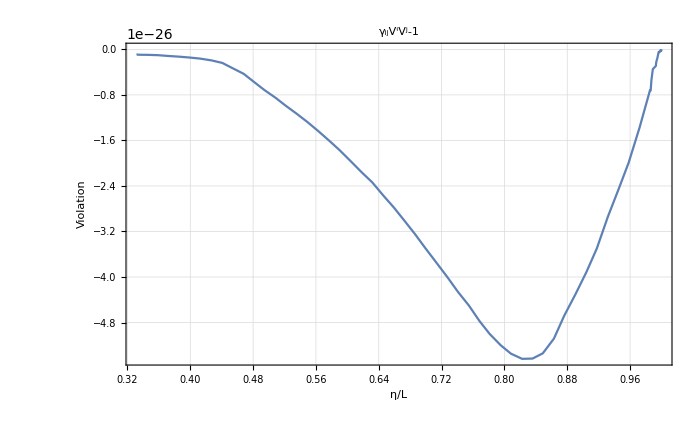

-Graphics-

```mathematica
TimeObject[Now]
EPN[η_]:=energy[η]/.geodesic;
lupPN[η_]:=EPN[η](nup[η]+Flatten[{0,VV[η]}]);
ldownPN[η_]:=EPN[η](ndown[η]+Flatten[{0,gg[η].VV[η]}]);
Plot[Evaluate[{gg[η].VV[η].VV[η]-1}/.geodesic/.param], {η, ηin,ETA0},PlotRange->All,WorkingPrecision->40,ImageSize->700,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","γ_ijV^iV^j-1",{},{}]]]
Plot[Evaluate[{gg4[η].lupPN[η].lupPN[η],lupPN[η].ldownPN[η]}/.geodesic/.param], {η, ηin,ETA0},PlotRange->All,WorkingPrecision->40,ImageSize->700,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","g_μνℓ^μℓ^ν",{"up-up","up-down"},{1,0.5}]]]
```

```mathematica
Join[geodesicPN,enerPN]>>"PN_geodesic_anl=046_k=100_bisect.m";
```

```mathematica
δPN[η_]:=(((2/3 𝒟[η]/((𝒽0)^2 Ωm0)ϕ''[x[η]])/(1-2/3 𝒟[η]/((𝒽0)^2 Ωm0)ϕ''[x[η]])+1/c^2 1/((1-2/3(𝒟[η]ϕ''[x[η]])/((𝒽0)^2 Ωm0))^2)(5/9(3-4 anl) 𝒟[η]/((𝒽0)^2 Ωm0)(ϕ'[x[η]])^2+20/9(2-anl) 𝒟[η]/((𝒽0)^2 Ωm0)(ϕ[x[η]]ϕ''[x[η]])+20/21( 2/3 𝒟[η]/((𝒽0)^2 Ωm0))^2((ϕ'[x[η]])^2 ϕ''[x[η]])))/.param)/.geodesic
```

```mathematica
δPN[ETA0]
```

3.53613032830699642011374501903384778642671×10^-6+0. ⅈ

### Compute the redshift

The  redshift is defined as z+1==(g_μν u^μ ℓ^ν|_𝒮)/(g_μν u^μ ℓ^ν|_𝒪). 
In 3+1, decomposing u^μ==Γ(n^μ+U^μ) and ℓ^μ=ℰ(n^μ+V^μ), the redshift becomes: z+1==ℰ_𝒮/ℰ_𝒪(1-γ_ij V^i U^j|_𝒮)/(1-γ_ij V^i U^j|_𝒪)((1-γ_ij U^i U^j|_𝒮)/(1-γ_ij U^i U^j|_𝒪))^(1/2). In synchronous-comoving coordinates U^i==0 and the redshift simplifies to z+1==ℰ_𝒮/ℰ_𝒪

```mathematica
zPN[η_]:=EPN[η]/EPN[ETA0]-1;
```

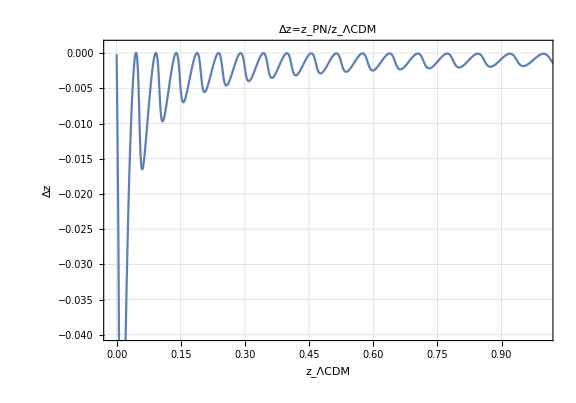

```mathematica
ParametricPlot[{(A[ETA0]/A[η]-1),zPN[η]/(A[ETA0]/A[η]-1)-1}, {η, ηin,ETA0},PlotRange->{{-0.01,1},{-0.04,0.001}},AspectRatio->0.7,ImageSize->Large, WorkingPrecision->40,Evaluate[StandardPlotStyle[16,24,"Δz","z_ΛCDM","Δz=z_PN/z_ΛCDM",{},{}]]]
```

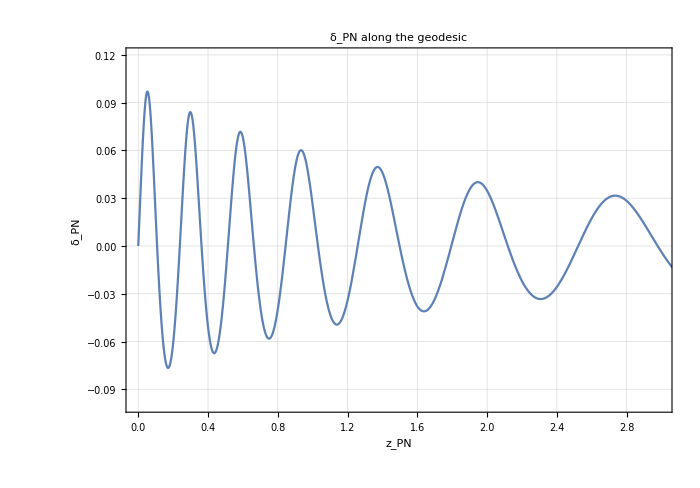

```mathematica
ParametricPlot[{zPN[η],δPN[η]/.Join[param,geodesic]},{η,ηin,ETA0},PlotRange->{{-0.01,3},{-0.1,0.12}},AspectRatio->0.7,ImageSize->700, WorkingPrecision->40,Evaluate[StandardPlotStyle[16,24,"δ_PN","z_PN","δ_PN along the geodesic",{},{}]]]
```

Compute the null geodesic

```mathematica
trajectoryPN[η_]:=Flatten[{x[η] ,y[η] ,z[η] }/.geodesic/.param];
Show[ParametricPlot3D[trajectoryPN[η],{η,ηin,ETA0},PlotRange->{{-2,2},{- 2,2},{-2,2}}, ImageSize->700, ViewPoint->{0,0,Infinity}, AxesLabel->{"X/L","Y/L","Z/L"}]/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]] ]
```

-Graphics3D-

## Parallel transport of a frame

```mathematica
Clear[transport2,vecbcframe,soltrans2,soldeviation,solGDE,tot1,tot2,totl,totu,Cu,Cl,Cf1,Cf2,Pu,Pl,P1,P2,F,F0,EE,EE0,OPT,ξ,ξA,ξbc,Ξ,ξ4,DA,DAbc,DAsolGDE,JMAP,frame,frame0]
```

```mathematica
frame0={fu0,f10,f20,fl0};
frame={{fu1,fu2,fu3},{f11,f12,f13},{f21,f22,f23},{fl1,fl2,fl3}};
Now
```

Sun 2 Aug 2020 20:42:21GMT+2.

#### set the SNF

```mathematica
(*Γl=1;
Β=0;
u[τ_]:=SetPrecision[(Γl/Sqrt[-g4[[1,1]]]{1,0,0,0}+Γl Β(Cos[0]Sin[π/2] 1/Sqrt[g4[[2,2]]]{0,1,0,0}+Sin[0]Sin[π/2] 1/Sqrt[g4[[3,3]]]{0,0,1,0}+Cos[π/2] 1/Sqrt[g4[[4,4]]]{0,0,0,1})),100]/.η->τ;*)
u[η_]:=SetPrecision[{1/A[η],0,0,0},50]
u[ETA0]//N
u[ηin]//N
```

{1.,0.,0.,0.}

{11.,0.,0.,0.}

```mathematica
gg4[ETA0].u[ETA0].lupPN[ETA0]/.Join[geodesic,param]
gg4[ETA0].u[ETA0].u[ETA0]/.η->ETA0
```

1.

-1.

Assuming f_1^μ=OverTilde[f_1]^μ+A u^μ+B k^μ and f_2^μ=OverTilde[f_2]^μ+C u^μ+D k^μ+E f_1^μ, the relations between the vector of the SNF can used to determine the constants A, B, C, D and E.

```mathematica
p1={0,0,1,0};
p2={0,0,0,1};
```

```mathematica
𝒻1=Re[(p1-(gg4[t].p1.lupPN[t])/(gg4[t].lupPN[t].u[t])u[t]-1/(gg4[t].lupPN[t].u[t])((gg4[t].p1.lupPN[t])/(gg4[t].lupPN[t].u[t])+gg4[t].p1.u[t])lupPN[t])/.Join[geodesic,param]/.t->ETA0]
s1=𝒻1/Sqrt[gg4[ETA0].𝒻1.𝒻1]/.Join[geodesic,param]
```

{0.,0.2500006803835864731146360260651826909539724693,0.7499993700156822017676704235658701471570609922,-0.3535542815256400748225920881293558834553446409}

{0.+0. ⅈ,0.2886756777529806267875282981471840600195221466+0. ⅈ,0.8660239489004209258361631763706962161839741874+0. ⅈ,-0.4082489763039183773070235626518331245639044413+0. ⅈ}

```mathematica
𝒻2=Re[(p2-(gg4[t].p2.lupPN[t])/(gg4[t].lupPN[t].u[t])u[t]-1/(gg4[t].lupPN[t].u[t])((gg4[t].p2.lupPN[t])/(gg4[t].lupPN[t].u[t])+gg4[t].p2.u[t])lupPN[t]-(gg4[t].p2.s1)s1)/.Join[geodesic,param]/.t->ETA0]
s2=𝒻2/Sqrt[gg4[ETA0].𝒻2.𝒻2]/.Join[geodesic,param]
```

{0.,0.4714061997059766615381508453198862046783378293,0.,0.333331093387210765045142423256400919718967136}

{0.+0. ⅈ,0.816501203514575753747572571016649142570996762+0. ⅈ,0.+0. ⅈ,0.577347601896709679388495173407914609774706373+0. ⅈ}

Initial conditions for the SN frame

```mathematica
(*u={1/A[η],0,0,0}=> fu0=α u^0 , fu^i=u^i+fu0 β^i/α;
f1=s1=> f10=α s1^0, f1^i=s1^i+f10 β^i/α;
f2=s2=> f20=α s2^0, f2^i=s2^i+f20 β^i/α;
ENW[η_]:=First[Evaluate[energy[η]/.enerNW]];
k[η_]:= Evaluate[(ENW[η](nup[η]+Flatten[{0,VV[η]}]))/.Join[geodesicNW]];
k => fl0=α k^0, fl^i=k^i+fl0 β^i/α ;*)
```

```mathematica
fu0in=(*Cu=*)SetPrecision[((-ndown[t].u[t])/.geodesic/.param)/.t->ETA0,50];
fuin=(*fu^μ=*)SetPrecision[((u[t]-(-ndown[t].u[t]) nup[t])/.geodesic/.param)/.t->ETA0,50];

f10in=(*C1=*)SetPrecision[((-ndown[t].s1)/.geodesic/.param)/.t->ETA0,50];
f1in=(*Subscript[f, 1]^μ=*)SetPrecision[((s1-(-ndown[t].s1) nup[t])/.geodesic/.param)/.t->ETA0,50];

f20in=(*C2=*)SetPrecision[((-ndown[t].s2)/.geodesic/.param)/.t->ETA0,50];
f2in=(*Subscript[f, 2]^μ=*)SetPrecision[((s2-(-ndown[t].s2) nup[t])/.geodesic/.param)/.t->ETA0,50];

fl0in=(*Ck=*)SetPrecision[((-ndown[t].lupPN[t])/.geodesic/.param)/.t->ETA0,50];(*SetPrecision[A[ηin],∞];*)
flin=(*fk^μ=*)SetPrecision[((lupPN[t]-(fl0in) nup[t])/.geodesic/.param)/.t->ETA0,50];
```

### Parallel transport the SNF

```mathematica
initialframePN={{fu0[ETA0]==fu0in,fu1[ETA0]==fuin[[2]],fu2[ETA0]==fuin[[3]] ,fu3[ETA0]==fuin[[4]]},{f10[ETA0]==f10in,f11[ETA0]==f1in[[2]],f12[ETA0]==f1in[[3]],f13[ETA0]==f1in[[4]]},{f20[ETA0]==f20in,f21[ETA0]==f2in[[2]],f22[ETA0]==f2in[[3]],f23[ETA0]==f2in[[4]] },{fl0[ETA0]==fl0in,fl1[ETA0]==flin[[2]],fl2[ETA0]==flin[[3]],fl3[ETA0]==flin[[4]]}};
```

```mathematica
Timing[soltransPN=Flatten[PTransportedFrame[g,K,α,β,geodesicPN,initialframePN,frame,frame0,param,η,ηin,ETA0,"SS",50,50,10,10]]]
```

{33636.6,{fu1→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],fu2→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],fu3→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],fu0→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],f11→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],f12→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],f13→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],f10→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],f21→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],f22→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],f23→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],f20→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],fl1→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],fl2→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],fl3→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>],fl0→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]}}

```mathematica
totPN=Flatten[Join[Flatten[tmpsoltransPN],geodesic]];
```

```mathematica
totPN=<<"PN_ptSNF_anl=046_k=500_bisect.m";
```

```mathematica
totPN//MatrixForm
```

(fu1→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
fu2→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
fu3→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
fu0→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
f11→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
f12→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
f13→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
f10→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
f21→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
f22→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
f23→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
f20→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
fl1→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
fl2→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
fl3→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
fl0→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
x→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
y→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
z→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
v1→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
v2→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
v3→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
energy→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>]
affine→InterpolatingFunction[{{0.33152767919537452707752036185026395786676771218311, 1.0000000000000000000000000000000000000000000000000}}, <>])

```mathematica
Cu[η_]:=fu0[η];
Cf1[η_]:=f10[η];
Cf2[η_]:=f20[η];
Cl[η_]:=fl0[η];
Pu[η_]:={fu1[η],fu2[η],fu3[η]};
P1[η_]:={f11[η],f12[η],f13[η]};
P2[η_]:={f21[η],f22[η],f23[η]};
Pl[η_]:={fl1[η],fl2[η],fl3[η]};
```

```mathematica
Show[ParametricPlot3D[trajectoryPN[η],{η,ηin,ETA0},PlotRange->{{-2,2},{-2,2},{-2,2}}]/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]] ,Graphics3D[{{Red,Arrowheads[0.02],Table[Arrow[{trajectoryPN[η],(trajectoryPN[η]+(Pu[η]/.totPN))}],{η,ηin,ETA0,0.05}]},{Green,Arrowheads[0.02],Table[Arrow[{trajectoryPN[η],(trajectoryPN[η]+(P1[η]/.totPN))}],{η,ηin,ETA0,0.05}]},{Blue,Arrowheads[0.02],Table[Arrow[{trajectoryPN[η],(trajectoryPN[η]+(P2[η]/.totPN))}],{η,ηin,ETA0,0.05}]},{Black,Arrowheads[0.02],Table[Arrow[{trajectoryPN[η],(trajectoryPN[η]+(Pl[η]/.totPN))}],{η,ηin,ETA0,0.05}]}}],Graphics3D[Sphere[{0,0,0},0.05]] , ImageSize->700,ViewPoint->{0,100,10},AxesLabel->{x,y,z},AxesStyle->Directive[Red,12]]
TimeObject[Now]
```

-Graphics3D-

06:50:18GMT+2.TimeObject[{6,50,18.575253},TimeZone→2.]

### Define the induced metric of the SNF “h”

```mathematica
Clear[F,F0,EE,EE0,Q,h]
```

```mathematica
(*((((gg4[ETA0].(Evaluate[Cu[ETA0]nup[ETA0]+Flatten[{0, Pu[ETA0]}]]).(Evaluate[Cl[ETA0]nup[ETA0]+Flatten[{0, Pl[ETA0]}]]))))/.totBG/.param)*)Q=Re[((gg4[ETA0].(Evaluate[Cu[ETA0]nup[ETA0]+Flatten[{0, Pu[ETA0]}]]).(Evaluate[Cl[ETA0]nup[ETA0]+Flatten[{0, Pl[ETA0]}]]))/.totPN/.param)]
h={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
Ih=Inverse[h];
```

1.

```mathematica
F[t_]:={{Pu[t][[1]],P1[t][[1]],P2[t][[1]],Pl[t][[1]]},{Pu[t][[2]],P1[t][[2]],P2[t][[2]],Pl[t][[2]]},{Pu[t][[3]],P1[t][[3]],P2[t][[3]],Pl[t][[3]]}};
F0[t_]:={Cu[t],Cf1[t],Cf2[t],Cl[t]};
TimeObject[Now]
```

06:50:25GMT+2.TimeObject[{6,50,25.540428},TimeZone→2.]

```mathematica
totPN>>"PN_ptSNF_anl=046_k=100_bisect.m"
```

#### Check SNF

-0.57735026630287451474075727918495279118

```mathematica
(gg4[t].u[t].s1)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].u[t].s2)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].lupN[t].s1)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].lupN[t].s2)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].s1.s2)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].s1.s1)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].s2.s2)/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].lupN[t].u[t])/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].u[t].u[t])/.Join[exactgeodesicBG,param]/.t->ηin
(gg4[t].lupN[t].lupN[t])/.Join[exactgeodesicBG,param]/.t->ηin
```

0.

0.

0.

«2 more identical outputs»

1.

1.

-0.0001

-1.

0.

```mathematica
Check of the relations: u^μ Subscript[u, μ]=-1,f1^μ Subscript[f1, μ]=1,f2^μ Subscript[f2, μ]=1,k^μ Subscript[k, μ]=0
```

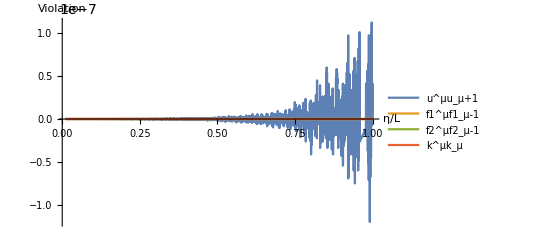

```mathematica
Plot[{(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+1)/.totBG/.param,(gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]])-1)/.totBG/.param,(gg4[η].(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]])-1)/.totBG/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μu_μ+1","f1^μf1_μ-1","f2^μf2_μ-1","k^μk_μ"},PlotRange->All(*{-10^-6,10^-6}*)]
```

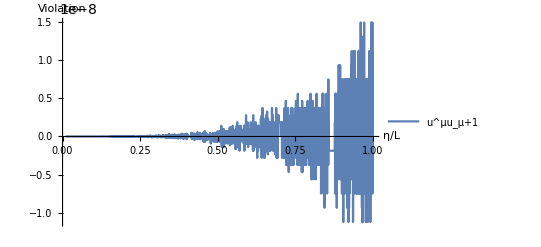

```mathematica
Plot[(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+1)/.totBG/.param,{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μu_μ+1","f1^μf1_μ-1","f2^μf2_μ-1","k^μk_μ"},PlotRange->All]
```

```mathematica
Check of the relations: u^μ Subscript[f1, μ]=0,u^μ Subscript[f2, μ]=0,k^μ Subscript[f1, μ]=0,k^μ Subscript[f2, μ]=0
```

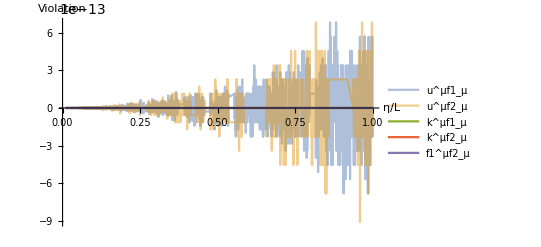

```mathematica
Plot[{(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μf1_μ","u^μf2_μ","k^μf1_μ","k^μf2_μ","f1^μf2_μ"},PlotRange->All(*{{tin,t0},{-10^-8,10^-8}}*),PlotStyle->{Opacity[.5],Opacity[.5],Thick,Thick,Thick}]
```

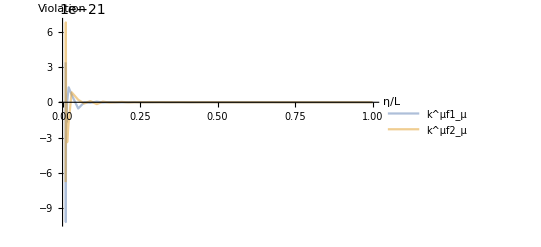

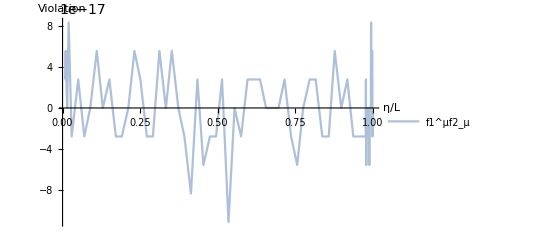

```mathematica
Plot[{(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totBG/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"k^μf1_μ","k^μf2_μ"},PlotRange->All(*{{tin,t0},{-10^-8,10^-8}}*),PlotStyle->{Opacity[.5],Opacity[.5],Thick,Thick,Thick}]
Plot[{(gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totBG/.param},{η,ηin,ETA0},AxesLabel->{"η/L","Violation"},PlotLegends->{"f1^μf2_μ"},PlotRange->All(*{{tin,t0},{-10^-8,10^-8}}*),PlotStyle->{Opacity[.5],Opacity[.5],Thick,Thick,Thick}]
```

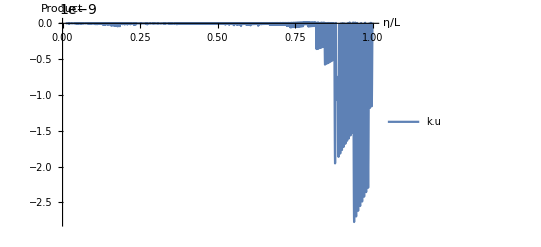

```mathematica
Plot[((((gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]])))/((gg4[ηin].(Evaluate[Cu[ηin]nup[ηin]+Flatten[{0, Pu[ηin]}]]).(Evaluate[Cl[ηin]nup[ηin]+Flatten[{0, Pl[ηin]}]]))))/.totBG/.param)-1,{η,ηin,ETA0},AxesLabel->{"η/L","Product"},PlotLegends->{"k.u"},PlotRange->All]
```

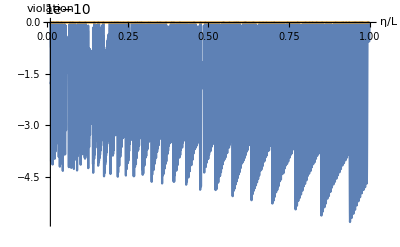

```mathematica
Plot[Evaluate[{(gg[η].VV[η].VV[η]-1),( gg[η].Pl[η].Pl[η]-Cl[η]^2) (*( (gg[η].Pl[η].Pl[η]-Cl[η]^2)/Cl[η]^2) *)}/.totBG/.param], {η, ηin,ETA0},PlotRange->Full,AxesLabel->{Style["η/L",Large],Style["violation",Large]}]
```

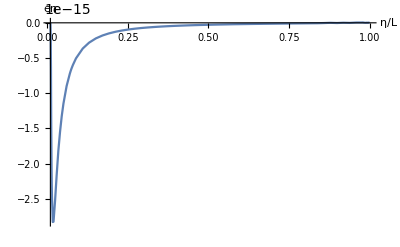

```mathematica
Plot[(A[ηin]^2/A[η]-Cl[η])/.totBG,{η, ηin,ETA0},PlotRange->Full,AxesLabel->{Style["η/L",Large],Style["en",Large]}]
```

## Optical Tidal Matrix

```mathematica
Clear[A,𝒟,ϕ,γN11,γPN11,γaa]
Now
```

Tue 4 Aug 2020 20:53:13GMT+2.

```mathematica
Timing[OPT=OpticalTidalMatrix[X,V,frame,frame0,Q,g,K,α,β,η]//Simplify;]
```

{67.5532,Null}

```mathematica
OPT//N//MatrixForm
```

(0. | 0. | 0. | 0.
(0.25 (2. A[η]^4 f13[η] fu3[η] v2[η]^2 (((γaa^(0,1)[η,x[η]])^2)/(2.+2. γ11[η,x[η]])-2. (((1.+γaa[η,x[η]]) A'[η])/A[η]+0.5 γaa^(1,0)[η,x[η]])^2)+2. A[η]^4 f12[η] fu2[η] v3[η]^2 (((γaa^(0,1)[η,x[η]])^2)/(2.+2. γ11[η,x[η]])-2. (((1.+γaa[η,x[η]]) A'[η])/A[η]+0.5 γaa^(1,0)[η,x[η]])^2)+12+(f13[η]-1. f10[η] v3[η]) (-1. fu3[η]+fu0[η] v3[η]) (4. (1.+γaa[η,x[η]]) A'[η]^2-2. A[η] A'[η] γaa^(1,0)[η,x[η]]+A[η] (-4. (1.+γaa[η,x[η]]) A''[η]+A[η] (((γaa^(1,0)[η,x[η]])^2)/(1.+γaa[η,x[η]])-2. γaa^(2,0)[η,x[η]])))))/A[η]^2 | -(0.25 (-(1. A[η]^4 f13[η]^2 v2[η]^2 (γaa^(0,1)[η,x[η]])^2)/(1.+γ11[η,x[η]])+25+(f13[η]-1. f10[η] v3[η])^2 (4. (1.+γaa[η,x[η]]) A'[η]^2-2. A[η] A'[η] γaa^(1,0)[η,x[η]]+A[η] (-4. (1.+γaa[η,x[η]]) A''[η]+A[η] (((γaa^(1,0)[η,x[η]])^2)/(1.+γaa[η,x[η]])-2. γaa^(2,0)[η,x[η]])))))/A[η]^2 | (0.25 (2. A[η]^4 f13[η] f23[η] v2[η]^2 (((γaa^(0,1)[η,x[η]])^2)/(2.+2. γ11[η,x[η]])-2. (((1.+γaa[η,1]) A'[η])/A[η]+0.5 γaa^(1,0)[η,x[η]])^2)+13+(f13[η]-1. f10[η] v3[η]) (1) (4. (1.+γaa[η,x[η]]) A'[η]^2-2. 2 γaa^1[η,1]+A[η] (-4. (1.+γaa[η,x[η]]) A''[η]+A[η] (1^2/1-1)))))/A[η]^2 | 0.
(0.25 (2. A[η]^4 f23[η] fu3[η] v2[η]^2 (1^2/(2.+2. γ11[η,x[η]])-2. (1/1+1)^2)+14))/A[η]^2 | (0.25 (2. 4 (1^2/(2.+1)-2. 1^2)+13+1))/A[η]^2 | -(0.25 (-1/1+25+1))/A[η]^2 | 0.
1 | (0.25 (1))/1^2 | 1/1^2 | 0.)
 |  |  |  |

The OPT’s components can have a complicated form and this cause the fail of finding a solution in NDSolve. 
There are some method which can be used to reduce the OPT’s components in a better shape and this depends case by case:
	- If the components are “good functions”, then we can use FunctionInterpolation[OPT[t][[i,j]], {t,ti,tf},InterpolationOrder→n] as components
	- alternatively, we need to discretize the function and then  interpolate. This case is very expensive and time consuming! to reduce the pain, we can use the symmetries of the Riemann tensor to reduce the number of fuctions that we need to interpolate. On top of that, we need to choose the correct step used to discretize the function.

#### Use the interpolation to make a better OPT

```mathematica
A[η_]=((Ωm0/ΩΛ)^(1/3)((1-JacobiCN[( 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3)) 𝒽0 η ,(2+Sqrt[3])/4])/(-1+√3+(1+√3) JacobiCN[( 3^(1/4)(ΩΛ)^(1/6)(Ωm0)^(1/3)) 𝒽0 η ,(2+Sqrt[3])/4])))/.param(*from 1109.2258*);
normalizzazione=5/2 Ωm0-((5/2 Ωm0)-(A[η]Sqrt[1+ΩΛ/Ωm0 A[η]^3]Hypergeometric2F1[3/2,5/6,11/6,-ΩΛ/Ωm0 A[η]^3])/.η->ETA0)/.param;
𝒟[η_]=(A[η]/(normalizzazione)Sqrt[1+ΩΛ/Ωm0 A[η]^3]Hypergeometric2F1[3/2,5/6,11/6,-ΩΛ/Ωm0 A[η]^3])/.param;
ϕ[x_]=(Amp Sin[ω  x])/.param;
γN11[η_,x_]:=(1-(2 𝒟[η] ϕ''[x])/(3 (𝒽0)^2 Ωm0))^2/.param
γPN11[η_,x_]:=((-(10 ϕ[x])/3+(4 anl-5)(10  𝒟[η] ϕ'[x]^2)/(9 (𝒽0)^2 Ωm0)+(anl-1)(40  𝒟[η] ϕ[x] ϕ''[x])/(9 (𝒽0)^2 Ωm0)+20/27(41/7-4anl)(𝒟[η]^2 ϕ'[x]^2 ϕ''[x])/((𝒽0)^4 Ωm0^2)+40/27(3-2 anl)(𝒟[η]^2 ϕ[x] ϕ''[x]^2)/((𝒽0)^4 Ωm0^2)-(80 𝒟[η]^3 ϕ'[x]^2 ϕ''[x]^2)/(189 (𝒽0)^6 Ωm0^3)))/.param;
γaa[η_,x_]:=((10/9((𝒟[η] ϕ'[x]^2)/((𝒽0)^2 Ωm0)-3 ϕ[x])))/.param;
```

```mathematica
Simpleℛll[t_]=Evaluate[(EPN[η])^2 OPT/.Join[{η->t},totPN,param]];
```

```mathematica
Timing[Table[{τ,A[τ]^5 Simpleℛll[τ]},{τ,ηin,ETA0,(ETA0-ηin)/9}];]
Now
```

{529.586,Null}

Tue 4 Aug 2020 21:05:17GMT+2.

```mathematica
step=(ETA0-ηin)/9999
```

0.0000668539174722097682690748713021038145947827070523941653461608575830287

```mathematica
Timing[TMP=Table[{τ,Simpleℛll[τ]},{τ,ηin,ETA0,step}];]
Now
```

{540546.,Null}

Tue 11 Aug 2020 03:50:07GMT+2.

```mathematica
Timing[tmp00=Table[{TMP[[i,1]],TMP[[i,2]][[1,1]]},{i,1,Length[TMP]}];
tmp01=Table[{TMP[[i,1]],TMP[[i,2]][[1,2]]},{i,1,Length[TMP]}];
tmp02=Table[{TMP[[i,1]],TMP[[i,2]][[1,3]]},{i,1,Length[TMP]}];
tmp03=Table[{TMP[[i,1]],TMP[[i,2]][[1,4]]},{i,1,Length[TMP]}];
tmp10=Table[{TMP[[i,1]],TMP[[i,2]][[2,1]]},{i,1,Length[TMP]}];
tmp11=Table[{TMP[[i,1]],TMP[[i,2]][[2,2]]},{i,1,Length[TMP]}];
tmp12=Table[{TMP[[i,1]],TMP[[i,2]][[2,3]]},{i,1,Length[TMP]}];
tmp13=Table[{TMP[[i,1]],TMP[[i,2]][[2,4]]},{i,1,Length[TMP]}];
tmp20=Table[{TMP[[i,1]],TMP[[i,2]][[3,1]]},{i,1,Length[TMP]}];
tmp21=Table[{TMP[[i,1]],TMP[[i,2]][[3,2]]},{i,1,Length[TMP]}];
tmp22=Table[{TMP[[i,1]],TMP[[i,2]][[3,3]]},{i,1,Length[TMP]}];
tmp23=Table[{TMP[[i,1]],TMP[[i,2]][[3,4]]},{i,1,Length[TMP]}];
tmp30=Table[{TMP[[i,1]],TMP[[i,2]][[4,1]]},{i,1,Length[TMP]}];
tmp31=Table[{TMP[[i,1]],TMP[[i,2]][[4,2]]},{i,1,Length[TMP]}];
tmp32=Table[{TMP[[i,1]],TMP[[i,2]][[4,3]]},{i,1,Length[TMP]}];
tmp33=Table[{TMP[[i,1]],TMP[[i,2]][[4,4]]},{i,1,Length[TMP]}];]
```

{1.02232,Null}

```mathematica
tmp[t_]=({{Interpolation[tmp00,InterpolationOrder->20][t],Interpolation[tmp01,InterpolationOrder->20][t],Interpolation[tmp02,InterpolationOrder->20][t],Interpolation[tmp03,InterpolationOrder->20][t]},{Interpolation[tmp10,InterpolationOrder->20][t],Interpolation[tmp11,InterpolationOrder->20][t],Interpolation[tmp12,InterpolationOrder->20][t], Interpolation[tmp13,InterpolationOrder->20][t]},{Interpolation[tmp20,InterpolationOrder->20][t],Interpolation[tmp12,InterpolationOrder->20][t],Interpolation[tmp22,InterpolationOrder->20][t], Interpolation[ tmp23,InterpolationOrder->20][t]},{Interpolation[tmp30,InterpolationOrder->20][t],Interpolation[tmp31,InterpolationOrder->20][t],Interpolation[tmp32,InterpolationOrder->20][t],Interpolation[tmp33,InterpolationOrder->20][t]}});
```

```mathematica
ℛab[t_]=tmp[t];
Now
```

Tue 11 Aug 2020 10:59:58GMT+2.

```mathematica
(Simpleℛll[t]/.t->0.9)//MatrixForm
(ℛab[t]/.t->0.9)//MatrixForm
```

(0 | 0 | 0 | 0
1.60310301408856814724778067043029490871915131+0. ⅈ | -26.84197864002102150724842378317254184343009774+0. ⅈ | -5.63687948204363369584498266211937486565882712+0. ⅈ | 0
4.53427718798399805449609236516872955680434831+0. ⅈ | -5.63687948204363369584498266211937486565882712+0. ⅈ | -40.79261141113030929637356509250311268432650816+0. ⅈ | 0
1.03317349355308735839235436999508321668098108+0. ⅈ | 1.60310301408856814724778067043029490871915131+0. ⅈ | 4.53427718798399805449609236516872955680434831+0. ⅈ | 0)

(0 | 0 | 0 | 0
1.603103014088568026315394645107327569438765+0. ⅈ | -26.841978640021021187826252067586174276273136+0. ⅈ | -5.636879482043633269497065891540990775359011+0. ⅈ | 0
4.534277187983997712446358552620559346372043+0. ⅈ | -5.636879482043633269497065891540990775359011+0. ⅈ | -40.792611411130307921789004587109763953207491+0. ⅈ | 0
1.033173493553087513007455125708490237513579+0. ⅈ | 1.603103014088568026315394645107327569438765+0. ⅈ | 4.534277187983997712446358552620559346372043+0. ⅈ | 0)

```mathematica
TMP>>"PN_res9999_TMP_anl=046_k=100_bisect.m"
```

## 𝒲 operators

```mathematica
Mxx={{MXX00,MXX01,MXX02,MXX03},{MXX10,MXX11,MXX12,MXX13},{MXX20,MXX21,MXX22,MXX23},{MXX30,MXX31,MXX32,MXX33}};
Mxl={{MXL00,MXL01,MXL02,MXL03},{MXL10,MXL11,MXL12,MXL13},{MXL20,MXL21,MXL22,MXL23},{MXL30,MXL31,MXL32,MXL33}};
Mlx={{MLX00,MLX01,MLX02,MLX03},{MLX10,MLX11,MLX12,MLX13},{MLX20,MLX21,MLX22,MLX23},{MLX30,MLX31,MLX32,MLX33}};
Mll={{MLL00,MLL01,MLL02,MLL03},{MLL10,MLL11,MLL12,MLL13},{MLL20,MLL21,MLL22,MLL23},{MLL30,MLL31,MLL32,MLL33}};
Now
```

Tue 11 Aug 2020 11:16:39GMT+2.

```mathematica
Mxleq=BGOequations[Mxl,Mll,ℛab[η],αα[η],EPN[η],param,η];
```

```mathematica
Mxlgrupbc=Flatten[Table[{Mxl[[i,j]][ETA0]==0,Mll[[i,j]][ETA0]==KroneckerDelta[i,j]},{i,1,Length[Mxl]},{j,1,Length[Mxl]}]];
```

```mathematica
Timing[Mxlgroupsol=SolveBGO[Mxleq, Mxlgrupbc,Mxl,Mll, totPN, param,η,ηin,ETA0,"SS",50,50,20,10,1000.];]
```

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{925.562,Null}

```mathematica
Mxxeq=BGOequations[Mxx,Mlx,ℛab[η],αα[η],EPN[η],param,η];
Now
```

Tue 11 Aug 2020 11:32:21GMT+2.

```mathematica
Mxxgrupbc=Flatten[Table[{Mxx[[i,j]][ETA0]==KroneckerDelta[i,j],Mlx[[i,j]][ETA0]==0},{i,1,Length[Mxx]},{j,1,Length[Mxx]}]];
```

```mathematica
Timing[Mxxgroupsol=SolveBGO[Mxxeq, Mxxgrupbc,Mxx,Mlx, totPN, param,η,ηin,ETA0,"SS",50,50,20,10,1000.];]
```

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{1475.64,Null}

```mathematica
hUU={{0,0,0,1/Q},{0,1,0,0},{0,0,1,0},{1/Q,0,0,1/Q^2}};
hDD={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
hUU.hDD//MatrixForm
```

(1. | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0. | 0 | 0 | 1.)

```mathematica
Now
functional[η_]:=Flatten[Table[{Mxx[[i,j]]->Mxx[[i,j]][η],Mxl[[i,j]]->Mxl[[i,j]][η],Mlx[[i,j]]->Mlx[[i,j]][η],Mll[[i,j]]->Mll[[i,j]][η]},{i,1,4},{j,1,4}]];
```

Tue 11 Aug 2020 11:56:56GMT+2.

```mathematica
BGO=Join[Mxlgroupsol,Mxxgroupsol];
```

```mathematica
MXX[η_]:=Mxx/.functional[η]/.BGO;
MLX[η_]:=Mlx/.functional[η]/.BGO;
MXL[η_]:=Mxl/.functional[η]/.BGO;
MLL[η_]:=Mll/.functional[η]/.BGO;
```

```mathematica
𝒲[η_]:={{MXX[η],MXL[η]},{MLX[η],MLL[η]}};
```

```mathematica
𝒲[ETA0]//N//MatrixForm
𝒲[ηin]//N//MatrixForm
```

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.))

((1. | 0. | 0. | 0.
0.000242422 | 0.287653 | -0.000119971 | 0.
0.000685675 | -0.000119971 | 0.287356 | 0.
0.0293712 | 0.000323055 | 0.000913742 | 1.) | (0.162302 | 0. | 0. | 0.
0.0000276294 | 0.0607994 | 4.47716×10^-7 | 0.
0.000078148 | 4.47716×10^-7 | 0.0608005 | 0.
-0.000937306 | 0.0000275862 | 0.0000780258 | 0.162302)
(0. | 0. | 0. | 0.
0.0169136 | -174.399 | 0.100998 | 0.
0.0478391 | 0.100998 | -174.149 | 0.
-2.80003 | 0.0470683 | 0.13313 | 0.) | (1. | 0. | 0. | 0.
0.00872071 | -33.3852 | 0.00715967 | 0.
0.024666 | 0.00715967 | -33.3675 | 0.
-0.483835 | 0.00911675 | 0.0257862 | 1.))

```mathematica
Join[XXgroup,XLgroup]>>"PN_res9999_BGO_anl=046_k=100_bisect.m"
```

### Forward to backwards transformation for 𝒲 operators

In the case when the initial conditions are given at the initial time, i.e. at the source, the BGO are integrated forward in time and they describe the optical properties as seen by the source: to indicate the fact that 𝒲 acts from the source 𝒮 to any point along the null geodesic p_λ, we write 𝒲(p_λ,𝒮). 
However, all observables are “seen” by the observer 𝒪, not by the source! Therefore, before of using these BGO to compute observables they need to be transformed in  𝒲(p_λ,𝒪). This can be done using the BGO properties as described in Grasso & Villa (2021) and in Grasso et. al. (2021).

The procedure to perform the transformations is encoded in this section: note that here we consider that all the quantities (meaning the geodesic and the parallel transported frame) were obtained giving the initial conditions at η_in.

Solve the GDE for BGO forward in time to obtain  𝒲(p_λ,𝒮)

```mathematica
Mxleq=BGOequations[Mxl,Mll,ℛll[η],αα[η],EBG[η],param,η];
Mxlgrupbc=Flatten[Table[{Mxl[[i,j]][ηin]==0,Mll[[i,j]][ηin]==KroneckerDelta[i,j]},{i,1,Length[Mxl]},{j,1,Length[Mxl]}]];
Timing[Mxlgroupsol=SolveBGO[Mxleq, Mxlgrupbc,Mxl,Mll, totBG, param,η,ηin,ETA0,"SS",60,50,20,10,1000.];]
```

```mathematica
Mxxeq=BGOequations[Mxx,Mlx,ℛll[η],αα[η],EBG[η],param,η];
Mxxgrupbc=Flatten[Table[{Mxx[[i,j]][ηin]==KroneckerDelta[i,j],Mlx[[i,j]][ηin]==0},{i,1,Length[Mxx]},{j,1,Length[Mxx]}]];
Timing[Mxxgroupsol=SolveBGO[Mxxeq, Mxxgrupbc,Mxx,Mlx, totBG, param,η,ηin,ETA0,"SS",60,50,20,10,1000.];]
```

```mathematica
hUU={{0,0,0,1/Q},{0,1,0,0},{0,0,1,0},{1/Q,0,0,1/Q^2}};
hDD={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
hUU.hDD//MatrixForm


functional[η_]:=Flatten[Table[{Mxx[[i,j]]->Mxx[[i,j]][η],Mxl[[i,j]]->Mxl[[i,j]][η],Mlx[[i,j]]->Mlx[[i,j]][η],Mll[[i,j]]->Mll[[i,j]][η]},{i,1,4},{j,1,4}]];
```

```mathematica
BGO=Join[Mxxgroupsol,Mxlgroupsol];
```

The block matrices of 𝒲(p_λ,𝒮) are:

```mathematica
MXX[η_]:=Mxx/.functional[η]/.BGO;
MLX[η_]:=Mlx/.functional[η]/.BGO;
MXL[η_]:=Mxl/.functional[η]/.BGO;
MLL[η_]:=Mll/.functional[η]/.BGO;
ℳ[η_]:={{MXX[η],MXL[η]},{MLX[η],MLL[η]}};
```

Then, 𝒲(p_λ,𝒪) is obtained as:
							𝒲(p_λ,𝒪) = 𝒲(p_λ,𝒮) 𝒲(𝒮,𝒪)
	where 𝒲(𝒮, 𝒪)= 𝒲^-1(𝒪,𝒮).
In other words, we need to compute the inverse of the 8x8 block matrix 𝒲^-1(𝒪,𝒮): this is not a simple task in general but, using the fact that 𝒲 is symplectic, we can find the inverse block components as:

```mathematica
WXX[η_]:=Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mll[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mll[[i,j]]->Mll[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WLX[η_]:=-Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mlx[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mlx[[i,j]]->Mlx[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WXL[η_]:=-Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mxl[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mxl[[i,j]]->Mxl[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WLL[η_]:=Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mxx[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mxx[[i,j]]->Mxx[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
```

Then, the previous components calculated at η_0 give  𝒲^-1(𝒪,𝒮), and finally we have:
							𝒲(p_λ,𝒪) = 𝒲(p_λ,𝒮) 𝒲^-1(𝒪,𝒮)

```mathematica
𝒲[η_]:=({{MXX[η].WXX[ETA0]+MXL[η].WLX[ETA0],MXX[η].WXL[ETA0]+MXL[η].WLL[ETA0]},{MLX[η].WXX[ETA0]+MLL[η].WLX[ETA0],MLX[η].WXL[ETA0]+MLL[η].WLL[ETA0]}})
```

```mathematica
𝒲[ETA0]//N//MatrixForm
ℳ[ηin]//N//MatrixForm
```

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0.000356027 | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0.000356027 | 0. | 0. | 1.))

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.))

## Observables

### Angular diameter distance

```mathematica
Now
Timing[tmpWAB=SetPrecision[Table[𝒲[η][[1,2]][[i,j]],{i,2,3},{j,2,3}],50];]
```

Tue 11 Aug 2020 12:20:17GMT+2.

{0.030289,Null}

```mathematica
Timing[detWxlAB[t_]=SetPrecision[Evaluate[Simplify[Sqrt[Abs[(Det[tmpWAB])]]]/.η->t],50];]
```

{0.839012,Null}

```mathematica
detWxlAB[ETA0]
```

0.

```mathematica
(*Uvel[η_]:=Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]/.totBG*)
Timing[
DangWxl[η_]=Evaluate[(gg4[ETA0].lupPN[ETA0].(nup[ETA0]))Evaluate[detWxlAB[η]]/.Join[param,totPN]];]
```

{0.163424,Null}

```mathematica
DangWxl[ETA0]
Now
```

0.

Tue 11 Aug 2020 12:20:27GMT+2.

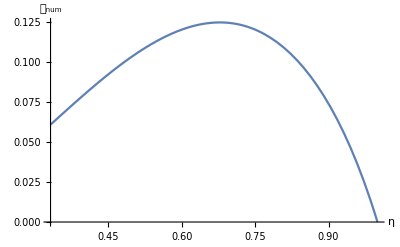

```mathematica
Plot[DangWxl[η] ,{η,ηin,ETA0},WorkingPrecision->30,AxesLabel->{"η","𝒟_num"}]
```

In ΛCDM the angular diameter distance as function of the redshift is:

```mathematica
χz[z_]:=Evaluate[1/(z+1)(1/(𝒽0 Ωm0^(1/3)ΩΛ^(1/6) 3^(1/4))(EllipticF[ArcCos[(2 Sqrt[3])/(1+Sqrt[3]+((Ωm0/ΩΛ)^(1/3)(1+z)))-1],(2+Sqrt[3])/4]-EllipticF[ArcCos[(2 Sqrt[3])/(1+Sqrt[3]+(Ωm0/ΩΛ)^(1/3))-1],(2+Sqrt[3])/4]))//.param];
```

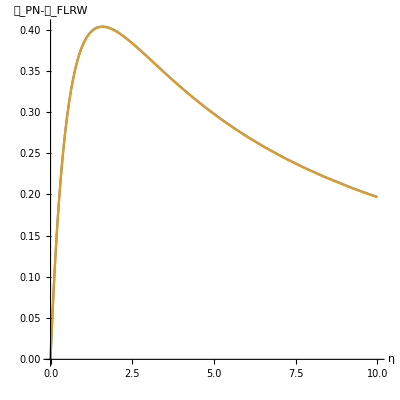

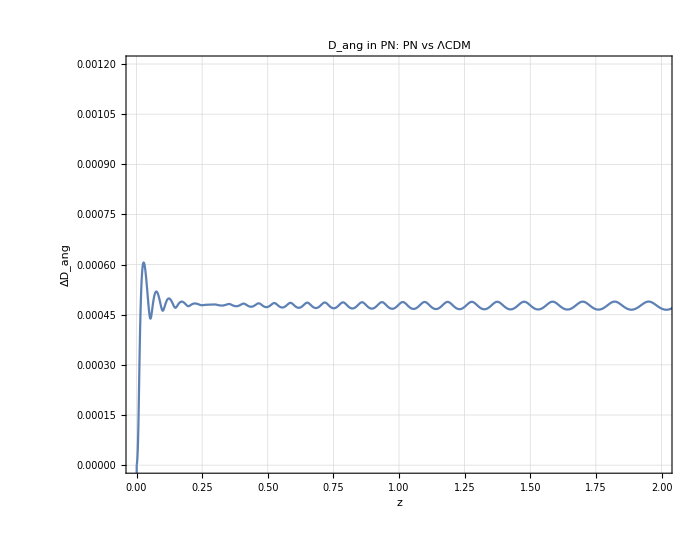

```mathematica
ParametricPlot[{{zPN[η],𝒽0 DangWxl[η] },{zPN[η], 𝒽0 χz[1/A[η]-1]}},{η,ηin,ETA0},AspectRatio->1, PlotRange->{{0,10}},AxesLabel->{"η","𝒟_PN-𝒟_FLRW"}]

ParametricPlot[{1/A[η]-1,SetPrecision[(DangWxl[η]/χz[1/A[η]-1]-1),70]},{η,ηin,ETA0},PlotRange->{{0,2},{0,0.0012}},Evaluate[StandardPlotStyle[18,24,"ΔD_ang","z","D_ang in PN: PN vs ΛCDM",{},{}]],AspectRatio->0.8, ImageSize->700]
```